# Two-point functions of the Q-Potts on the torus

Computes the topological corrections derived in 1.
The parameter w corresponds to the torus aspect ratio M/N and q is the elliptic nome q = e^(-2Pi w). Q and β are different parametrisations of the central charge c.
The partition function, the structure constants and the Virasoro related quantities are computed in the notebooks Potts-torus-partition.nb and CFT-general.nb.

## Identity contribution

c_Tis the coefficient of (r/N)^2. This is the contribution of the second level descendant of the identity, the stress-energy tensor. For Q = 1 it needs to be regularised. For any Q, we actually compute 2 c_T, taking into account the contributions of both T and T̄.

```mathematica
cT[w_,Q_]:=Module[{β=Sqrt[t[Q]/(t[Q]+1)]},
If[Q==1,First[Re[2 Delta[β+0.001,0,1/2]/c[β+0.001] 2(Pi ⅈ)^2 q D[Zq[β+0.001,q,q],q]/Zq[β+0.001,q,q]/.q->Exp[-2Pi w]]],First[Re[2 Delta[β,0,1/2]/c[β] 2(Pi ⅈ)^2 q D[Zq[β,q,q],q]/Zq[β,q,q]/.q->Exp[-2Pi w]]]]]
```

### Q = 1

```mathematica
wtab ={1,2,5};
epstab = Table[1/n,{n,10,1000,50}]//N  ; (*regularisation parameter*)
cTtab = Table[2cT[w,Q[Sqrt[2/3]+eps]],{w,wtab},{eps,epstab}];
TableForm[{cTtab}, TableHeadings->{None,{"M/N=1","M/N=2","M/N=5"}}]
```

General::munfl: 0.00186744^116.04 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.00186744^120.375 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.00186744^120.97 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

M/N=1 | M/N=2 | M/N=5
-3.51498×10^-16
-1.44866×10^-15
-2.77703×10^-15
-2.05519×10^-15
-4.53771×10^-15
-6.78077×10^-15
-6.76386×10^-15
-6.3018×10^-15
-5.39444×10^-15
-1.61669×10^-14
-1.57051×10^-14
-1.23316×10^-14
-5.37811×10^-15
-5.82359×10^-15
-1.25382×10^-14
3.35729×10^-15
-1.07401×10^-14
-2.28167×10^-14
-1.20766×10^-14
-2.97381×10^-14 | 0.198881
0.186148
0.181428
0.179471
0.178403
0.177732
0.177271
0.176935
0.176679
0.176478
0.176316
0.176182
0.17607
0.175974
0.175892
0.17582
0.175758
0.175702
0.175653
0.175608 | 0.413365
0.347243
0.335135
0.330308
0.327716
0.3261
0.324995
0.324193
0.323584
0.323105
0.32272
0.322402
0.322136
0.32191
0.321716
0.321547
0.321399
0.321268
0.321151
0.321046

```mathematica
cTtabinv = Table[2 w^-2 cT[1/w,Q[Sqrt[2/3]+eps]],{w,wtab},{eps,epstab}];
TableForm[{cTtabinv}, TableHeadings->{None,{"N/M=1","N/M=2","N/M=5"}}]
```

General::munfl: 0.00186744^116.04 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.00186744^120.375 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.00186744^120.97 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

N/M=1 | N/M=2 | N/M=5
-3.51498×10^-16
-1.44866×10^-15
-2.77703×10^-15
-2.05519×10^-15
-4.53771×10^-15
-6.78077×10^-15
-6.76386×10^-15
-6.3018×10^-15
-5.39444×10^-15
-1.61669×10^-14
-1.57051×10^-14
-1.23316×10^-14
-5.37811×10^-15
-5.82359×10^-15
-1.25382×10^-14
3.35729×10^-15
-1.07401×10^-14
-2.28167×10^-14
-1.20766×10^-14
-2.97381×10^-14 | -0.198881
-0.186148
-0.181428
-0.179471
-0.178403
-0.177732
-0.177271
-0.176935
-0.176679
-0.176478
-0.176316
-0.176182
-0.17607
-0.175974
-0.175892
-0.17582
-0.175758
-0.175702
-0.175653
-0.175608 | -0.413366
-0.347226
-0.335113
-0.330282
-0.327686
-0.326065
-0.324957
-0.324151
-0.323538
-0.323055
-0.322666
-0.322344
-0.322075
-0.321845
-0.321647
-0.321474
-0.321322
-0.321187
-0.321066
-0.320958

## Energy contribution

c_(1,2)is the coefficient of (r/N)^(2 Δ_(1,2)). This is the dominant correction on a square torus ie when M = N.

```mathematica
c12[w_,Q_]:=Module[{β=Sqrt[t[Q]/(t[Q]+1)],q=Exp[-2Pi w]},
If[Q==1,Re[(2Pi)^(2Delta[β,1,2])q^(2Delta[β,0,1/2])Pi Sqrt[3](4/9*Gamma[7/4]/Gamma[1/4])^2 F[q,β,Delta[β,0,1/2],Delta[β,1,2]]^2//N],First[Re[(2Pi)^(2Delta[β,1,2])(Q-1)constzam[1,2,0,1/2,0,1/2,t[Q]]^2/Zq[β,q,q] q^(2Delta[β,0,1/2]-c[β]/12)F[q,β,Delta[β,0,1/2],Delta[β,1,2]]^2]]]];
```

### M ≠ N, Q = 1

To be compared with the contribution of the stress-energy tensor.

```mathematica
c12tab = Table[c12[w,1],{w,wtab}];
TableForm[{c12tab}, TableHeadings->{None,{"M/N=1","M/N=2","M/N=5"}}]
```

M/N=1 | M/N=2 | M/N=5
0.355402 | 0.185569 | 0.0260479

```mathematica
c12tabinv = Table[w^(-2Delta[Sqrt[2/3],1,2])c12[1/w,1],{w,wtab}];
TableForm[{c12tabinv}, TableHeadings->{None,{"N/M=1","N/M=2","N/M=5"}}]
```

N/M=1 | N/M=2 | N/M=5
0.355402 | 0.185557+0. ⅈ | 0.0248901+0. ⅈ

## V_(1,3) contribution

This contribution becomes non-negligible and visible numerically near Q = 3. The computation of c_(1,3) is not exact since the fusion rule of V_(1,3)allows every channel in the spectrum. We included in the formula below the most dominant terms.

```mathematica
c13[w_,Q_]:=Module[{β = Sqrt[t[Q]/(t[Q]+1)],q=Exp[-2Pi w]},If[Q==1,0,
(2Pi)^(2Delta[β,1,3])constzam[1,3,0,1/2,0,1/2,t[Q]]/Zq[β,q,q] q^(-c[β]/12)((Q-1)constzam[1,3,0,1/2,0,1/2,t[Q]] q^(2Delta[β,0,1/2])F[q,β,Delta[β,0,1/2],Delta[β,1,3]]^2+
constzam[1,3,1,2,1,2,t[Q]] q^(2Delta[β,1,2])F[q,β,Delta[β,1,2],Delta[β,1,3]]^2+
(Q-1)constzam[1,3,0,3/2,0,3/2,t[Q]] q^(2Delta[β,0,3/2])F[q,β,Delta[β,0,3/2],Delta[β,1,3]]^2)//N]]
```

```mathematica
c13tab = Re[Table[c13[1,Q],{Q,2.,3.75,0.25}]];
```

General::munfl: 0.00186744^133.333 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.00186744^114.083 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
TableForm[Transpose@{Table[Q,{Q,2,3.75,0.25}],c13tab},TableHeadings->{None,{"Q","c13"}}]
```

Q | c13
2. | 0.00173282
2.25 | 0.0201829
2.5 | 0.0379292
2.75 | 0.0539287
3. | 0.0693684
3.25 | 0.0851117
3.5 | 0.102118
3.75 | 0.122246

## Two-point connectivity

Here rP2 is the rescaled two-point connectivity r^(4 Δ_(0,1/2))p_12(r,N). It takes as argument the central charge, the aspect ratio w, the parameter s = r/N, and the parameters T and X = 0, 1 which allow to include or not the contributions of the stress-energy tensor and the field V_(1,3), respectively (note that when w = 1 the contribution of the stress-energy tensor vanishes anyway).

```mathematica
rP2[Q_,w_,s_,T_,X_]:=Module[{β},
β = Sqrt[B[Q]];
Re[(1+c12[w,Q] s^(2Delta[β,1,2])+2T cT[w,Q] s^2+X c13[w,Q] s^(2Delta[β,1,3]))]];
```

### Q = 1, M/N = 1/2

A case where the contribution of the stress-energy tensor becomes dominant.

```mathematica
P2tab = Table[{s,rP2[1,0.5,s,0,0]},{s,0.001,0.5,0.005}]; (*not including the contribution of T*)
P2tabwT = Table[{s,rP2[1,0.5,s,1,0]},{s,0.001,0.5,0.005}];
```

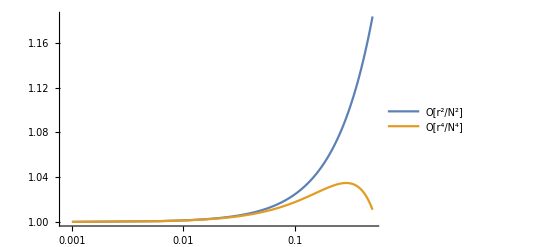

```mathematica
ListLogLinearPlot[{P2tab,P2tabwT},PlotLegends->{"O[r^2/N^2]","O[r^4/N^4]"},Joined->True]
```

### Q ~ 3

```mathematica
P2tab = Table[{s,First[rP2[3.25,1,s,0,0]]},{s,0.001,0.5,0.005}];
P2tabw13 = Table[{s,First[rP2[3.25,1,s,0,1]]},{s,0.001,0.5,0.005}]; (*including the contribution of Subscript[V, 1,3]*)
```

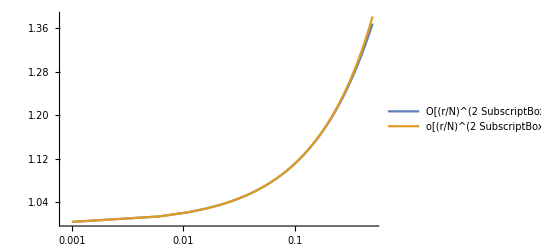

```mathematica
ListLogLinearPlot[{P2tab,P2tabw13},Joined->True,PlotLegends->{"O[(r/N)^(2 SubscriptBox[Δ, 1, 3])]","o[(r/N)^(2 SubscriptBox[Δ, 1, 3])]"}]
```

## References

1	N. Javerzat, M. Picco, R. Santachiara [arXiv:1907.11041]